## The QNMs of Myers-Perry Black Holes

### Computing the QN frequencies

```mathematica
Remove["Global`*"];
Unprotect[In,Out];
Clear[In,Out];
Off[General::spell1];


a1=0.7;
rh=√(M/(1+a1^2));
M=1;
l=0;
m=-2;
j=2;
Alm=(2j+l+Abs[m])(2j+l+Abs[m]+1+1);

winit=2*(0.37-0.08 ⅈ);

ie=0;While[ie<7,NITMAX=3;
σ=((rh^2+a1^2rh^2)w1/rh-m*a1*rh)/(2rh^2);
λ=Alm-2m*w1/rh+w1^2a1^2;
(*intial recurrence relation*)
γ1=Function[n,-8n^2+4n-11+8l^2a1^2-8λ+64w1*σ-ⅈ*4(4n-1)(2w1+σ)];
β1=Function[n,-6-4n-4(n+1)^2a1^2-4λ+32w1*σ+ⅈ(2m*a1-(16n+10+2a1^2)w1)];
α1=Function[n,4(n+1)(n+1+2ⅈ*σ)];
δ1=Function[n,-8+4n-4l^2a1^2-4λ+32w1*σ-4ⅈ(4(n-1)w1-σ)];
ϵ1=Function[n,2(2n-3)(2n-3+4ⅈ*σ)];
(*Four term recurrence relation after gauss elimination*)
α2=Function[n,If[n<0,0,α1[n]]];
β2=Function[n,If[n< 2,β1[n],
β1[n]-(α2[n-1]ϵ1[n])/δ2[n-1]]];
γ2=Function[n,If[n<2,γ1[n],
γ1[n]-(β2[n-1]ϵ1[n])/δ2[n-1]]];
Δ2:=Function[k,Module[{d2},
For[{n=2;d2=δ1[2];},
n<k,
{
d2= δ1[n]-(γ2[n-1]ϵ1[n])/d2;n++;}];d2]];
δ2=Function[k,If[k<2,δ1[k],Δ2[k]]];

(*three term recurrence relation after gauss elimination*)
α=Function[n,α2[n]];
β=Function[n,If[n< 1,β2[n],β2[n]-(α[n-1]δ2[n])/γ[n-1]]];
Γ:=Function[μ,Module[{g},
For[{n=1;g=γ2[1];},
n<μ,
{
g= γ2[n]-(β[n-1]δ2[n])/g;n++;}];g]];
γ=Function[μ,If[μ==0,γ2[μ],Γ[μ]]];

Leaver31[w1_]:=Module[{Rn},
For[{n=NITMAX;Rn=-1.0;},
n>0,
{
Rn=γ[n]/(β[n]-α[n]*Rn);n--;}
];Rn];Leaver33[w1_]:=β[0]/α[0]-Leaver31[w1];wang=FindRoot[Leaver33[w1]==0,{w1,winit}][[1]][[2]];witer[ie]=wang;γang=Function[n,-wang^2a1^2];
βang=Function[n,2((l+Abs[m]+2n)(l+1+Abs[m]+2n+1)-Sep)];
αang=Function[n,-8(n+1)(2l+1+2n+1)];
Leaver31Ang[Sep_]:=Module[{Rn},
For[{n=NITMAX;Rn=-1.0;},
n>0,
{
Rn=γang[n]/(βang[n]-αang[n]*Rn);n--;}
];Rn];
Leaver33Ang[Sep_]:=βang[0]/αang[0]-Leaver31Ang[Sep];

Alm=FindRoot[Leaver33Ang[Sep]==0,{Sep,Alm}][[1]][[2]];
ie=ie+1];
witer[6]
(*Table[witer[n],{n,0,6}];*)
(*Print[l,"  ",m,"  ",j,"  ",If[IntegerQ[(j-(l+m))/2],If[(j-(l+m))/2≥ 0,witer[6],"  "]," "]];,{l,0,1},{m,0,1},{j,0,1}]*)
```

0.772571-0.12813 ⅈ

```mathematica
(*Do[
Print[j,"  ",l,"   ",m,"  ",Table[witer[n],{n,0,6}],{j,0,3},{l,0,3},{m,0,3}]*)
```

{wang,wang,wang,wang,wang,wang,wang}

```mathematica
(*As you see the roots rapidly converge to the final value 2Mw=0.879684-0.173764 ⅈ [BCW], even with only seven recursions*)
```

### Angular wavefunctions

```mathematica
(*We write the spheroidal wavefunctions as Subscript[Y, lm](θ,ϕ)=e^imϕ Subscript[S, lm](θ). Here we compute the Subscript[S, lm](θ) functions, normalizing them to 1:∫_-1^1|Subscript[S, lm](θ)|^2 ⅆcosθ=1. The relevant eqs are (18)-(20) in [1]. *)
```

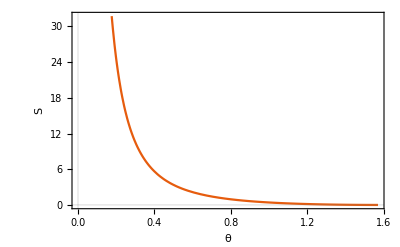

```mathematica
Sep=Alm;Nmax=150;w=wang;sima=(w*rplus-ar*m)/br;ae[0]=1;ae[1]=-βang[0]/αang[0];i=1;While[i<Nmax,ae[i+1]=(-βang[i]*ae[i]-γang[i]*ae[i-1])/(αang[i]);i=i+1];Sang=(Sin[θ])^m(Cos[θ])^j*Sum[ae[i]*(Cos[θ]^2)^(i),{i,0,Nmax-1}]/.θ->θ;(*Normalization=1/Sqrt[NIntegrate[2Sin[2θ]*Sang*Conjugate[Sang],{θ,0,π/2},MaxRecursion->12,PrecisionGoal->16,AccuracyGoal->16]];*)SangNormal=Sang;
Re[SangNormal];
Plot[Re[SangNormal],{θ,0π,π/2},AxesLabel->{None,None},FrameLabel->{{HoldForm[S],None},{HoldForm[θ],None}},PlotTheme->"Scientific"]
```

```mathematica
(*SangNormal is the angular wavefunction Subscript[S, lm](cosθ)- Let's plot its real part:*)
```

```mathematica
(*...and evaluate it at θ=1.3:*)
```

### Radial Wavefunctions

```mathematica
(*We now use Leaver's expansion to compute the radial wavefunctions themselves. The wavefunction is in-going at the horizon, ψ==e^(iw r_+)(r_+-r_-)^(-1-s+iw+iσ_+)(r-r_+)^(-s-iσ_+), r -> r_+  *)
```

Re[(2.71828^((0.156403+0.943043 ⅈ) r) ((-0.819232+r)/(0.819232+r))^(0.11652+1.55703 ⅈ) (1.+((7.21727-5.4784 ⅈ) (-0.819232+r)^3)/(0.819232+r)^3+((4.69713-1.80286 ⅈ) (-0.819232+r)^2)/(0.819232+r)^2+((1.76233-0.851029 ⅈ) (-0.819232+r))/(0.819232+r)))/(-1.+1.22066 r)^(3/2)]

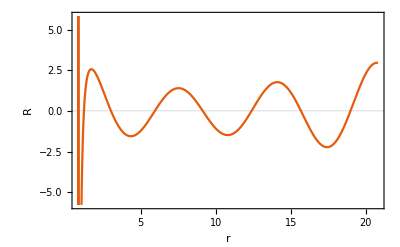

```mathematica
Nmax=4;
w1=witer[6];
w=w1/rh;
be[0]=1;
be[1]=-β[0]/α[0];
i=1;
While[i<Nmax,be[i+1]=(-β[i]*be[i]-γ[i]*be[i-1])/(α[i]);
i=i+1];
Psi=Exp[I*w*r](r/rh-1)^(-3/2)*((r-rh)/(r+rh))^(I*σ)*Sum[be[i]*((r-rh)/(r+rh))^i,{i,0,Nmax-1}]/.r->r;
(*Psi=Exp[I*w*r]*((r+rh)/rh)^(-3/2-ⅈ*σ)*((r-rh)/rh)^(ⅈ*σ)*Sum[be[i]*((r-rh)/(r+rh))^(i),{i,0,Nmax-1}]/.r->r;*)
(*R=10;Psi/.r->R*)
rh;
N[Re[Psi]]
Plot[Re[Psi],{r,rh,rh+20},AxesLabel->{None,None},FrameLabel->{{HoldForm[R],None},{HoldForm[r],None}},PlotTheme->"Scientific"]
```

(-19.7566+20.0091 ⅈ) ⅇ^((0.156403+0.943043 ⅈ) t)

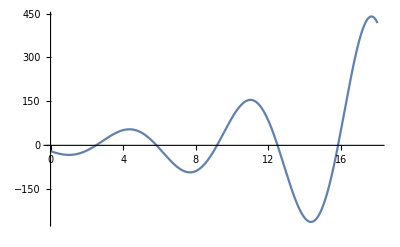

```mathematica
r=1.1rh;θ=π/4;
Φ=Exp[I*w*t]Sang*Psi
Plot[Re[Φ],{t,0,18}]
```

```mathematica
(*A sanity check is to compare with the direct numerical integration of Teukolsky's wavefunction, with the same boundary conditions at the horizon:*)
```

```mathematica
r1=rplus+10^(-6);r2=150;Delta=(r-rplus)*(r-rminus);Kr=w*(r^2+ar^2)-ar*m;VgLe=2*I*s*w*r-ar^2*w^2-Alm+1/Delta*((r^2+ar^2)^2*w^2-2*ar*m*w*r+ar^2*m^2+I*s*(ar*m*(2*r-1)-w*(r^2-ar^2)));Vg=(Kr^2-2*I*s*Kr*(r-1/2))/Delta+4*I*s*w*r-Alm+2*ar*w*m-ar^2*w^2;sol=NDSolve[{Delta*D[y[r],{r,2}]+(s+1)*(2*r-1)*D[y[r],{r,1}]+Vg*y[r]==0,y[r1]==(rplus-rminus)^(-1-s+I*w+I*sima)*Exp[I*w*r1]*(r1-rplus)^(-s-I*sima),y'[r1]==(rplus-rminus)^(-1-s+I*w+I*sima)*Exp[I*w*r1]*(-s-I*sima)*(r1-rplus)^(-s-I*sima-1)},y,{r,r1,r2},
            AccuracyGoal -> 20, PrecisionGoal -> 20,WorkingPrecision -> 30,MaxSteps->340000];
```

NDSolve::precw: The precision of the differential equation (((-2.834677320695924` - 0.22863486622673967` ⅈ) - (1.3901113962622083` + 7.0374707584056075` ⅈ) r + Times[« 3 »] + Power[« 2 »]/Plus[« 2 »] Plus[« 2 »]) y[r] - (-1 + 2 r) SuperscriptBox[« 1 »SuperscriptBox[) is less than WorkingPrecision (30.). More…

```mathematica
y[R]/.sol
```

{-1970.833618667500512614008613-2863.235215367325145808685161 ⅈ}

```mathematica
(*the two methods agree to a good precision*)
```

## References

```mathematica
[1] E. Leaver, "An analytic representation for te quasi-normal modes of kerr black holes". Proc. R. Soc. Lond.A402: 285(1985).
```

```mathematica
[2]E. Berti, V. Cardoso and C. M. Will, "On gravitational-wave spectroscopy of massive black holes with the space interferometer LISA", Phys. Rev. D73:064030 (2006). [arXiv: gr-qc/0512160].
```

```mathematica
[3]E. Berti, V. Cardoso and M. Casals, "Eigenvalues and eigenfunctions of spin-weighted spheroidal harmonics in four and higher dimensions", Phys. Rev. D73:024013 (2006); Erratum-ibid.D73:109902 (2006). [arXiv: gr-qc/0511111].
```